```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210224_impacts_in_time_windows"];
```

```mathematica
datafull=Import["datafull_manipulated.mx",HeaderLines->1];
```

Handling Width and Thickness Null/Zero Values

Calculation through density for one unknown feature in a row

```mathematica
datacol[x_]:=datafull[[All,x]]
densityfunction[weight_,denom1_,denom2_,denom3_]:=N@(weight/(denom1*denom2*denom3))
rowfunction[rownum_,density_]:={(datacol@9)[[rownum]],(datacol@10)[[rownum]],(datacol@12)[[rownum]],(datacol@11)[[rownum]],density}
```

```mathematica
MapThread[TableView[{{"WIDTH","THICKNESS","LENGTH","WEIGHT","DENSITY"},rowfunction[#1,dens=densityfunction[(datacol@11)[[#1]],(datacol@9)[[#1]],(datacol@10)[[#1]],(datacol@12)[[#1]]]],rowfunction[#2,dens],rowfunction[#3,dens],row5=rowfunction[#4,dens]},Alignment->Center,Background->{{{None,None,None,None,Red}},{1->Lighter@Gray}}]&,{{16742},{16746},{16747},{16748}}]
Print["NA = ",widthforNA=densityfunction[row5[[4]],row5[[2]],row5[[3]],row5[[5]]]]
datafull[[16746;;16748,9]]=widthforNA;
```

{WIDTHTHICKNESSLENGTHWEIGHTDENSITY1.54e116.5e935000.160.4.566861709718853e-24NA6.5e922000.160.4.566861709718853e-24NA6.5e922000.160.4.566861709718853e-24NA6.5e922000.160.4.566861709718853e-24}

NA = 2.45×10^11

```mathematica
(* *
If there is one NA value in a row, it is calculated by the common density value. 
* *)
```

```mathematica
Partition[Range[47897,47909],1]
```

{{47897},{47898},{47899},{47900},{47901},{47902},{47903},{47904},{47905},{47906},{47907},{47908},{47909}}

```mathematica
MapThread[TableView[{{"WIDTH","THICKNESS","LENGTH","WEIGHT","DENSITY"},rowfunction[#1,dens=densityfunction[(datacol@11)[[#1]],(datacol@9)[[#1]],(datacol@10)[[#1]],(datacol@12)[[#1]]]],rowfunction[#2,dens],rowfunction[#3,dens],row5=rowfunction[#4,dens]},Alignment->Center,Background->{{{None,None,None,None,Red}},{1->Lighter@Gray}}]&,{{16742},{16746},{16747},{16748}}]
Print["NA = ",widthforNA=densityfunction[row5[[4]],row5[[2]],row5[[3]],row5[[5]]]]
datafull[[16746;;16748,9]]=widthforNA;
```

{WIDTHTHICKNESSLENGTHWEIGHTDENSITY1.54e116.5e935000.160.4.566861709718853e-242.45e116.5e922000.160.4.566861709718853e-242.45e116.5e922000.160.4.566861709718853e-242.45e116.5e922000.160.4.566861709718853e-24}

NA = 2.45×10^11

```mathematica
datafull=Delete[Delete[datafull,459203],459202]; (* The last two rows are deleted because all features have Null values *)
```

Handling two Null/Zero features in a row by looking back and forth patterns in same HEAT_ID and SEQUENCE _ID groups

```mathematica
densityfunction2[weight_,denom1_,denom2_,denom3_]:=If[denom1=="NA"||denom1==0,"NA",If[denom2=="NA"||denom2==0,"NA",If[denom3=="NA"||denom3==0,"NA",weight/(denom1*denom2*denom3)]]]
rowfunction2[rownum_]:={(datacol@2)[[rownum]],(datacol@13)[[rownum]],(datacol@14)[[rownum]],(datacol@9)[[rownum]],(datacol@10)[[rownum]],(datacol@12)[[rownum]],(datacol@11)[[rownum]],densityfunction2[(datacol@11)[[rownum]],(datacol@9)[[rownum]],(datacol@10)[[rownum]],(datacol@12)[[rownum]]]}
heading={"SEQUENCE_ID","HEAT_ID","STEEL_GRADE","WIDTH","THICKNESS","LENGTH","WEIGHT","DENSITY"};
```

```mathematica
TableView[Partition[Flatten@Join[heading,Table[rowfunction2[i],{i,{47919,47920,47921,47951,47952,47953,47967,47968,47969,47978,47979,47980,47981,47982,47983,47984,47985,48276,48277,48278,48284,48286,48292,48293,48294,48339,48340,48341,48347,48348,48349,48350,48351,48352,48353,48354}}]],8],Alignment->Center,Background->{{None,None,Red,Red,Red,Red,None,Red},{1->Lighter@Gray}}]
```

SEQUENCE_IDHEAT_IDSTEEL_GRADEWIDTHTHICKNESSLENGTHWEIGHTDENSITY69317022321341.24e665.3.01e91.85e97.625532756815579e-969317022321341.24e665.3.01e91.85e97.625532756815579e-969317022321341.24e665.3.01e91.85e97.625532756815579e-969317022321341.22e665.3.43e92.08e97.647086937819624e-969317022321341.22e665.3.43e92.08e97.647086937819624e-969317022321341.22e665.3.43e92.08e97.647086937819624e-969317022321341.22e665.3.45e92.08e97.602755999049656e-969317022321341.22e665.3.45e92.08e97.602755999049656e-969317022321341.22e665.3.45e92.08e97.602755999049656e-969317022321NANANANA1.7e8NA69317022321NANANANA1.7e8NA69317022321NANANANA1.7e8NA69317022321NANANANA1.7e8NA69317022321NANANANA1.7e8NA69317022321NANANANA1.7e8NA69317022321NANANANA1.7e8NA69317022321NANANANA1.7e8NA69317022321341.24e665.3.3e92.02e97.594555981652755e-969317022321341.24e665.3.3e92.02e97.594555981652755e-969317022321341.24e665.3.3e92.02e97.594555981652755e-969317022321341.23e665.3.28e91.99e97.588584328620022e-969317022321341.23e665.3.28e91.99e97.588584328620022e-969317022321341.22e665.3.3e92.e97.642630593450266e-969317022321341.22e665.3.3e92.e97.642630593450266e-969317022321341.22e665.3.3e92.e97.642630593450266e-969317022321341.26e665.2.89e91.78e97.520353541114786e-969317022321341.26e665.2.89e91.78e97.520353541114786e-969317022321341.26e665.2.89e91.78e97.520353541114786e-969317022321340001.7e8NA69317022321340001.7e8NA69317022321340001.7e8NA69317022321340001.7e8NA69317022321340001.7e8NA69317022321340001.7e8NA69317022321340001.7e8NA69317022321340001.7e8NA

```mathematica
(* *
1- NA values in Steel Grade Feature are converted to "34" considering all steel grade values are "34" in the same sequence and heat id.
2- NA values in Thickness Feature are converted to "65" considering all thickness values are "65" in the same sequence and heat id.
3- Zero values in Width, Thickness, Length Features are at the end of the relevant sequence and heat group. Therefore they will be removed from the evaluation dataset.
* *)
```

```mathematica
densityrelation[weight1_,weight2_,length1_]:=N@weight2*length1/weight1
```

```mathematica
manipulator[data_,seq_,heat_,newwidth_,newthick_,newlength_,newstgr_,evaluationpart_]:=Module[{initialdata,filtercon,part,pos},
initialdata=data;
filtercon=Select[initialdata,#[[2]]==seq&&#[[13]]==heat&];
part=Join[filtercon[[All,1;;2]],filtercon[[All,9;;14]],2];
pos=Take[Sort@Join[If[MemberQ[part[[All,3]],"NA"],Position[part[[All,3]],"NA"],{}],
If[MemberQ[part[[All,3]],0],Position[part[[All,3]],0],{}]],evaluationpart];
initialdata[[part[[Flatten@pos,1]],9]]=newwidth;
initialdata[[part[[Flatten@pos,1]],10]]=newthick;
initialdata[[part[[Flatten@pos,1]],12]]=newlength;
initialdata[[part[[Flatten@pos,1]],14]]=newstgr;
initialdata]
```

```mathematica
datafull1=manipulator[datafull,693,17022341,1220000.0,65.,densityrelation[2080000000.0,10000000.0,3430000000.0],34,All];
```

```mathematica
datafull2=manipulator[datafull1,693,17022321,1220000.0,65.,densityrelation[2080000000.0,10000000.0,3430000000.0],34,8];
```

```mathematica
datafull3=manipulator[datafull2,259,17003161,1850000.0,65.,densityrelation[2200000000.0,2820000000.0,2410000000.0],30,All];
```

```mathematica
datafull4=manipulator[datafull3,259,17003141,1850000.0,65.,densityrelation[2640000000.0,65300000.0,2890000000.0],30,All];
```

```mathematica
datafull5=manipulator[datafull4,259,17003121,1870000.0,65.,densityrelation[2140000000.0,325000000.0,2320000000.0],30,All];
```

```mathematica
datafull6=manipulator[datafull5,259,17003101,1860000.0,65.,densityrelation[2190000000.0,435000000.0,2390000000.0],30,All];
```

```mathematica
datafull7a=manipulator[datafull6,323,17004401,1840000.0,66.,densityrelation[2100000000.0,335000000.0,2290000000.0],30,7];
```

```mathematica
datafull7b=manipulator[datafull7a,323,17004401,1840000.0,66.,densityrelation[2190000000.0,335000000.0,2380000000.0],30,-7];
```

```mathematica
datafull8=manipulator[datafull7b,714,17023421,1.84*10^6,65.,densityrelation[2.62*10^9,2.4*10^7,2.88*10^9],41,All];
```

```mathematica
datafull9=manipulator[datafull8,714,17023441,1.85*10^6,65.,densityrelation[3.52*10^9,1.9*10^8,3.85*10^9],41,All];
```

```mathematica
datafull10=manipulator[datafull9,714,17023461,1.84*10^6,65.,densityrelation[2.64*10^9,1.0*10^7,2.91*10^9],41,All];
```

```mathematica
datafull11=manipulator[datafull10,714,17023501,1.84*10^6,65.,densityrelation[2.07*10^9,1.30*10^8,2.28*10^9],35,All];
```

```mathematica
datafull12=manipulator[datafull11,714,17023521,1.84*10^6,65.,densityrelation[2.08*10^9,8.00*10^7,2.29*10^9],34,All];
```

```mathematica
datafull13=manipulator[datafull12,714,17023541,1.84*10^6,65.,densityrelation[3.53*10^9,1.10*10^8,3.88*10^9],34,All];
```

```mathematica
(*weightcorrection*)datafull13[[51111;;51115,11]]=1.10*10^8;
```

```mathematica
datafull14=manipulator[datafull13,714,17023561,1.84*10^6,65.,densityrelation[2.18*10^9,3.0*10^7,2.41*10^9],34,-7];
```

```mathematica
datafull15=manipulator[datafull14,714,17023561,1.84*10^6,65.,densityrelation[3.52*10^9,3.0*10^7,3.88*10^9],34,7];
```

```mathematica
datafull16=manipulator[datafull15,714,17023601,1.84*10^6,65.,densityrelation[2.1*10^9,1.8*10^8,2.32*10^9],34,All];
```

```mathematica
(*weightcorrection*)datafull16[[50883;;50887,11]]=2.0*10^7;
```

```mathematica
datafull17=manipulator[datafull16,714,17023621,1.84*10^6,65.,densityrelation[2.08*10^9,1.2*10^8,2.29*10^9],34,All];
```

```mathematica
datafull18=manipulator[datafull17,714,17023641,1.84*10^6,65.,densityrelation[3.43*10^9,1.0*10^7,3.79*10^9],26,All];
```

```mathematica
datafull19=manipulator[datafull18,714,17023661,1.84*10^6,65.,densityrelation[2.16*10^9,1.7*10^8,2.39*10^9],26,All];
```

```mathematica
datafull20=manipulator[datafull19,714,17023681,1.84*10^6,65.,densityrelation[2.16*10^9,8.0*10^7,2.39*10^9],26,All];
```

```mathematica
datafull21=manipulator[datafull20,714,17023701,1.84*10^6,65.,densityrelation[2.17*10^9,3.0*10^7,2.4*10^5],26,All];
```

```mathematica
datafull22=manipulator[datafull21,714,17023721,1.84*10^6,65.,densityrelation[2.1*10^9,1.0*10^7,2.32*10^9],26,All];
```

```mathematica
datafull23=manipulator[datafull22,714,17023741,1.84*10^6,65.,densityrelation[2.18*10^9,2.0*10^7,2.41*10^9],41,All];
```

```mathematica
(*weightcorrection*)datafull23[[51158;;51163,11]]=2.0*10^7;
```

```mathematica
manipulator2[data_,seq_]:=Module[{initialdata,filtercon,part,pos,newwidth,newthick,firstlength,firstweight,newlength,newstgr},
initialdata=data;
filtercon=Select[initialdata,#[[2]]==seq&];
part=Join[filtercon[[All,1;;2]],filtercon[[All,9;;14]],2];
pos=Split[Flatten@Take[Sort@Join[If[MemberQ[part[[All,3]],"NA"],Position[part[[All,3]],"NA"],{}],
If[MemberQ[part[[All,3]],0],Position[part[[All,3]],0],{}]],All],#2-#1==1&];
newwidth=Table[part[[pos[[i]][[1]]-1,3]],{i,Length@pos}];
newthick=Table[part[[pos[[i]][[1]]-1,4]],{i,Length@pos}];
firstlength=Table[part[[pos[[i]][[1]]-1,6]],{i,Length@pos}];
firstweight=Table[part[[pos[[i]][[1]]-1,5]],{i,Length@pos}];
newlength=Table[N@part[[pos[[i]][[1]],5]]*firstlength[[i]]/firstweight[[i]],{i,Length@pos}];
newstgr=Table[part[[pos[[i]][[1]]-1,8]],{i,Length@pos}];
Table[initialdata[[part[[pos[[i]],1]],9]]=newwidth[[i]],{i,Length@pos}];
Table[initialdata[[part[[pos[[i]],1]],10]]=newthick[[i]],{i,Length@pos}];
Table[initialdata[[part[[pos[[i]],1]],12]]=newlength[[i]],{i,Length@pos}];
Table[initialdata[[part[[pos[[i]],1]],14]]=newstgr[[i]],{i,Length@pos}];
initialdata]
```

```mathematica
(*weight corrections*)
datafull23[[63465;;63470,11]]=84.5*10^8;
datafull23[[63739;;63743,11]]=93.5*10^8;
datafull23[[63918;;63924,11]]=84.5*10^8;
datafull23[[63968;;63975,11]]=84.5*10^8;
datafull23[[64048;;64054,11]]=85.0*10^8;
```

```mathematica
datafull24=manipulator2[datafull23,792];
```

```mathematica
(*weight corrections*)
datafull24[[64506;;64512,11]]=83.0*10^8;
```

```mathematica
datafull25=manipulator2[datafull24,793];
```

```mathematica
(*length correction*)
datafull25[[64647;;64650,12]]=9.5*10^9;
```

```mathematica
(*weight corrections*)
datafull25[[65255;;65258,11]]=85.0*10^8;
```

```mathematica
datafull26=manipulator2[datafull25,795];
```

```mathematica
(*width, thickness, length corrections*)
datafull26[[68017;;68023,9]]=1.53*10^6;
datafull26[[68017;;68023,10]]=73;
datafull26[[68017;;68023,12]]=2.3*10^6;
```

```mathematica
(*weight corrections*)
datafull26[[68043;;68047,11]]=85.5*10^8;
datafull26[[68110;;68116,11]]=85*10^8;
```

```mathematica
datafull27=manipulator2[datafull26,853];
```

```mathematica
(*width corrections*)
datafull27[[68322;;68328,9]]=1.52*10^6;
```

```mathematica
datafull28=manipulator2[datafull27,862];
```

```mathematica
(*width corrections*)
datafull28[[72340;;72345,9]]=1.53*10^6;
datafull28[[72388;;72395,9]]=1.53*10^6;
datafull28[[72400;;72404,9]]=1.53*10^6;
datafull28[[72410;;72434,9]]=1.53*10^6;
datafull28[[72624;;72646,9]]=1.53*10^6;
datafull28[[72652;;72656,9]]=1.53*10^6;
datafull28[[72760;;72762,9]]=1.33*10^6;
datafull28[[72874;;72882,9]]=1.53*10^6;
datafull28[[73004;;73022,9]]=1.53*10^6;
datafull28[[73027;;73030,9]]=1.53*10^6;
datafull28[[73078;;73084,9]]=1.45*10^6;
```

```mathematica
(*length corrections*)
datafull28[[72364;;72369,12]]=2.84*10^9;
datafull28[[72887;;72891,12]]=4.04*10^9;
```

```mathematica
(*weight corrections*)
datafull28[[72405;;72409,11]]=84.5*10^8;
datafull28[[72692;;72697,11]]=2.19*10^9;
```

```mathematica
datafull29=manipulator2[datafull28,877];
```

```mathematica
(*weight corrections*)
datafull29[[83448;;83454,11]]=2.0*10^7; (* above/left items` density is 7.42*10^-11 *)
datafull29[[83514;;83520,11]]=4.0*10^7;
```

```mathematica
(*width, thickness, weight,length and/or st.gr. corrections*)
datafull29[[83549;;83554,9]]=1.54*10^6;
datafull29[[83549;;83554,10]]=76;
datafull29[[83549;;83554,11]]=1.5*10^9;
datafull29[[83549;;83554,12]]=2.36*10^9;

datafull29[[83573;;83579,9]]=1.54*10^6;
datafull29[[83573;;83579,10]]=67;
datafull29[[83573;;83579,11]]=4.0*10^7;
datafull29[[83573;;83579,12]]=2.7*10^9;
datafull29[[83573;;83579,14]]=30;
```

```mathematica
datafull30=manipulator2[datafull29,972];
```

```mathematica
(* weight corrections *)
datafull30[[105577;;105584,11]]=2.24*10^9;
datafull30[[105636;;105642,11]]=2.63*10^9;
datafull30[[105658;;105691,11]]=2.25*10^9;
datafull30[[105728;;105735,11]]=1.83*10^9; 
datafull30[[105809;;105817,11]]=1.50*10^9;
datafull30[[105902;;105915,11]]=1.82*10^9;
```

```mathematica
(* width, thickness, weight,length corrections *)
datafull30[[252504;;252511,9]]=1.21*10^6;
datafull30[[252504;;252511,10]]=67;
datafull30[[252504;;252511,11]]=1.96*10^9;
datafull30[[252504;;252511,12]]=3.20*10^9;

datafull30[[105792;;105799,11]]=1.96*10^9;
```

```mathematica
datafull31=manipulator2[datafull30,1165];
```

```mathematica
(* weight corrections *)
datafull31[[116114;;116120,11]]=2.5*10^9;
datafull31[[116212;;116218,11]]=1.72*10^9;
datafull31[[116289;;116302,11]]=1.71*10^9;
datafull31[[116317;;116323,11]]=1.83*10^9;
datafull31[[116382;;116386,11]]=4.51*10^9;
datafull31[[116407;;116410,11]]=2.5*10^9;
datafull31[[116452;;116458,11]]=2.05*10^9;
datafull31[[116492;;116498,11]]=2.07*10^9;
```

```mathematica
(* width, thickness, weight, length, st.gr. corrections *)
datafull31[[116336;;116339,9]]=1.74*10^6;
datafull31[[116336;;116339,10]]=66;
datafull31[[116336;;116339,11]]=2.5*10^9;
datafull31[[116336;;116339,12]]=2.86*10^9;
datafull31[[116336;;116339,14]]=41;
```

```mathematica
datafull32=manipulator2[datafull31,1203];
```

```mathematica
(* weight corrections *)
datafull32[[120293;;120298,11]]=2.18*10^9;
datafull32[[120311;;120316,11]]=2.19*10^9;
datafull32[[120330;;120336,11]]=0.5*10^9;
datafull32[[120343;;120348,11]]=2.19*10^9;
datafull32[[120367;;120372,11]]=2.19*10^9;
datafull32[[120386;;120392,11]]=2.19*10^9;
datafull32[[120442;;120448,11]]=0.5*10^9;
datafull32[[120636;;120699,11]]=2.18*10^9;
datafull32[[120726;;120791,11]]=2.18*10^9;
datafull32[[120869;;120927,11]]=2.18*10^9;
datafull32[[120984;;120990,11]]=2.19*10^9;
datafull32[[121005;;121018,11]]=2.17*10^9;
datafull32[[121039;;121045,11]]=2.18*10^9;
datafull32[[121287;;121292,11]]=2.26*10^9;
datafull32[[121311;;121316,11]]=1.59*10^9;
datafull32[[121619;;121625,11]]=2.17*10^9;
datafull32[[121640;;121646,11]]=1.86*10^9;
```

```mathematica
datafull33=manipulator2[datafull32,1279];
```

```mathematica
(* weight corrections *)
datafull33[[128141;;128147,11]]=1.56*10^9;
datafull33[[128201;;128207,11]]=1.92*10^9;
datafull33[[128240;;128245,11]]=2.17*10^9;
datafull33[[128275;;128279,11]]=3.12*10^9;
datafull33[[128326;;128329,11]]=3.06*10^9;
datafull33[[128347;;128351,11]]=3.06*10^9;
datafull33[[128392;;128396,11]]=3.07*10^9;
datafull33[[128446;;128450,11]]=3.12*10^9;
datafull33[[128500;;128504,11]]=3.12*10^9;
datafull33[[128519;;128536,11]]=3.12*10^9;
datafull33[[128562;;128596,11]]=3.06*10^9;
```

```mathematica
(* length corrections *)
datafull33[[128338;;128341,12]]=3.8*10^9;
datafull33[[128831;;128838,12]]=2.04*10^9;
```

```mathematica
(* width, thickness, weight, length, st.gr. corrections *)
datafull31[[128808;;128815,9]]=1.28*10^6;
datafull31[[128808;;128815,10]]=66;
datafull31[[128808;;128815,11]]=1.0*10^7;
datafull31[[128808;;128815,12]]=1.57*10^7;
datafull31[[128808;;128815,14]]=30;
```

```mathematica
datafull34=manipulator2[datafull33,1347];
```

```mathematica
(* length corrections *)
datafull34[[157142;;157148,12]]=1.7*10^9;
```

```mathematica
(* width corrections *)
datafull34[[157419;;157425,9]]=1.86*10^6;
```

```mathematica
(* weight corrections *)
datafull34[[157482;;157488,11]]=3.0*10^9;
datafull34[[157603;;157609,11]]=2.12*10^9;
datafull34[[157659;;157665,11]]=2.12*10^9;
datafull34[[157721;;157724,11]]=3.75*10^9;
datafull34[[157875;;157879,11]]=3.0*10^9;
datafull34[[158043;;158044,11]]=2.04*10^9;
```

```mathematica
datafull35=manipulator2[datafull34,1584];
```

```mathematica
(* weight corrections *)
datafull35[[243134;;243140,11]]=2.16*10^9;
datafull35[[243226;;243232,11]]=4.5*10^9;
datafull35[[243336;;243341,11]]=4.0*10^9;
datafull35[[243728;;243731,11]]=3.65*10^9;
datafull35[[243823;;243829,11]]=2.5*10^9;
datafull35[[243852;;243855,11]]=3.65*10^9;
datafull35[[243896;;243903,11]]=2.0*10^9;
datafull35[[243961;;243966,11]]=1.91*10^9;
datafull35[[244174;;244178,11]]=3.1*10^9;
```

```mathematica
(* length corrections *)
datafull35[[243261;;243266,12]]=2.32*10^9;
datafull35[[243668;;243688,12]]=2.81*10^9;
datafull35[[243768;;243795,12]]=2.81*10^9;
datafull35[[243830;;243836,12]]=2.72*10^9;
datafull35[[243837;;243843,12]]=2.81*10^9;
```

```mathematica
(* width, thickness, length, st.gr. corrections *)
datafull35[[243541;;243546,9]]=1.85*10^6;
datafull35[[243541;;243546,10]]=65;
datafull35[[243541;;243546,12]]=4.62*10^8;
datafull35[[243541;;243546,14]]=30;
```

```mathematica
(* width, thickness, length, st.gr. corrections *)
datafull35[[244184,9]]=1.43*10^6;
datafull35[[244184,10]]=65;
datafull35[[244184,12]]=1.42*10^10;
datafull35[[244184,14]]=31;
```

```mathematica
(* width, thickness, weight, length, st.gr. corrections *)
datafull35[[244186;;244190,9]]=1.43*10^6;
datafull35[[244186;;244190,10]]=65;
datafull35[[244186;;244190,11]]=3.10*10^9;
datafull35[[244186;;244190,12]]=4.39*10^9;
datafull35[[244186;;244190,14]]=31;
```

```mathematica
(* width corrections *)
datafull35[[243635;;243640,9]]=1.78*10^6;
```

```mathematica
datafull36=manipulator2[datafull35,2289];
```

```mathematica
(* weight corrections *)
datafull36[[253466;;253472,11]]=1.65*10^9;
datafull36[[253596;;253602,11]]=3.01*10^9;
datafull36[[253821;;253833,11]]=2.09*10^9;
datafull36[[253834;;253839,11]]=2.5*10^9;
datafull36[[254024;;254029,11]]=2.13*10^9;
datafull36[[254310;;254316,11]]=0.5*10^9;
```

```mathematica
(* width, thickness, length, st.gr. corrections *)
datafull36[[254113,9]]=1.22*10^6;
datafull36[[254113,10]]=65;
datafull36[[254113,12]]=1.73*10^10;
datafull36[[254113,14]]=26;
```

```mathematica
(* width, thickness, length corrections *)
datafull36[[254373;;254380,9]]=1.23*10^6;
datafull36[[254373;;254380,10]]=65;
datafull36[[254373;;254380,12]]=4.93*10^7;
```

```mathematica
(* width corrections *)
datafull36[[254303;;254309,9]]=1.23*10^6;
```

```mathematica
datafull37=manipulator2[datafull36,2403];
```

```mathematica
(* width and weight corrections *)
datafull37[[261200;;261204,9]]=1.25*10^6;
datafull37[[261200;;261204,11]]=2.13*10^9;
datafull37[[261775;;261802,9]]=0.957*10^6;
datafull37[[261803;;261810,11]]=2.5*10^9;
datafull37[[261811;;261818,9]]=0.957*10^6;
```

```mathematica
(* length corrections *)
datafull37[[261537;;261543,12]]=3.29*10^9;
```

```mathematica
(* weight corrections *)
datafull37[[261544;;261550,11]]=2.0*10^9;
```

```mathematica
datafull38=manipulator2[datafull37,2446];
```

```mathematica
(* width, thickness, weight, length, st.gr. corrections *)
datafull38[[275873;;275877,9]]=1.64*10^6;
datafull38[[275873;;275877,10]]=66;
datafull38[[275873;;275877,11]]=4.0*10^9;
datafull38[[275873;;275877,12]]=4.99*10^9;
datafull38[[275873;;275877,14]]=31;

datafull38[[275880;;275884,9]]=1.64*10^6;
datafull38[[275880;;275884,10]]=66;
datafull38[[275880;;275884,11]]=4.0*10^9;
datafull38[[275880;;275884,12]]=4.99*10^9;
datafull38[[275880;;275884,14]]=31;

datafull38[[275890;;275894,11]]=4.0*10^9;
```

```mathematica
datafull39=manipulator2[datafull38,2585];
```

```mathematica
(* width, thickness, length, st.gr. corrections *)
datafull39[[283081;;283086,9]]=1.85*10^6;
datafull39[[283081;;283086,10]]=65;
datafull39[[283081;;283086,12]]=3.08*10^8;
datafull39[[283081;;283086,14]]=30;
```

```mathematica
datafull40=manipulator2[datafull39,2646];
```

```mathematica
(* width, thickness, length, st.gr. corrections *)
datafull40[[299776;;299780,9]]=1.87*10^6;
datafull40[[299776;;299780,10]]=78;
datafull40[[299776;;299780,12]]=9.17*10^8;
datafull40[[299776;;299780,14]]=71;
```

```mathematica
datafull41=manipulator2[datafull40,2853];
```

```mathematica
(* width corrections *)
datafull41[[50650;;50655,9]]=1.85*10^6;
datafull41[[50662;;50667,9]]=1.85*10^6;
```

```mathematica
(* weight corrections *)
datafull41[[50945;;50951,11]]=0.5*10^9;
```

```mathematica
datafull42=manipulator2[datafull41,714];
```

```mathematica
(* width, thickness, length corrections *)
datafull42[[16743;;16748,9]]=1.54*10^11;
datafull42[[16743;;16745,10]]=6.5*10^9;
datafull42[[16743;;16745,12]]=21000;
```

```mathematica
(* width, thickness, weight, length corrections *)
datafull42[[16763;;16767,9]]=1.54*10^6;
datafull42[[16763;;16767,10]]=65;
datafull42[[16763;;16767,11]]=0.147*10^9;
datafull42[[16763;;16767,12]]=1.926*10^8;

datafull42[[16940;;16945,11]]=4.47*10^7;
datafull42[[17031;;17037,11]]=5.47*10^7;
datafull42[[17129;;17135,11]]=1.55*10^8;
```

```mathematica
datafull43=manipulator2[datafull42,398];
```

```mathematica
(* Export["ccm1_data_modified_numbered_slx.mx",datafull43] *)
```

```mathematica
3.0*10^7/(1.43*10^6*65*7.5755*10^(-9))
```

4.2605×10^7

```mathematica
0.147*10^9/(2.03*10^9)*2.66*10^9
```

1.92621×10^8

```mathematica
2.8*10^8/(2.38*10^9)*2.62*10^9
```

3.08235×10^8

```mathematica
filtercon=Select[datafull25,#[[2]]==793&];
part=Join[filtercon[[All,1;;2]],filtercon[[All,9;;14]],2]
```

below rows could not be reasoned with a logical density relation, so they were eliminated.

```mathematica
NApos=Complement[Position[datafull[[All,10]],0],Position[datafull[[All,9]],0]]
```

{{252553},{252554},{252555},{252556},{252557},{252558},{252559},{252560},{420845},{420846},{420847},{420848},{420849},{420850},{420851},{420852}}

```mathematica
NApos2=Partition[{385278,385287,385288,385289,385306,386693,386707},1];
```

```mathematica
NApos3=Partition[Flatten@{379146,Range[379211,379215],447783},1];
```

```mathematica
datafull[[All,9]]=ReplacePart[datafull[[All,9]],{NApos->"NA"}];
datafull[[All,10]]=ReplacePart[datafull[[All,10]],{NApos->"NA"}];
datafull[[All,11]]=ReplacePart[datafull[[All,11]],{NApos->"NA"}];
datafull[[All,12]]=ReplacePart[datafull[[All,12]],{NApos->"NA"}];
```

```mathematica
datafull[[All,9]]=ReplacePart[datafull[[All,9]],{NApos2->"NA"}];
datafull[[All,10]]=ReplacePart[datafull[[All,10]],{NApos2->"NA"}];
datafull[[All,11]]=ReplacePart[datafull[[All,11]],{NApos2->"NA"}];
datafull[[All,12]]=ReplacePart[datafull[[All,12]],{NApos2->"NA"}];
```

```mathematica
datafull[[All,9]]=ReplacePart[datafull[[All,9]],{NApos3->"NA"}];
datafull[[All,10]]=ReplacePart[datafull[[All,10]],{NApos3->"NA"}];
datafull[[All,11]]=ReplacePart[datafull[[All,11]],{NApos3->"NA"}];
datafull[[All,12]]=ReplacePart[datafull[[All,12]],{NApos3->"NA"}];
```

below rows were reasoned with a logical density relation, so they were manipulated.

```mathematica
manupos1=Complement[Position[datafull[[All,9]],0],Position[datafull[[All,10]],0]]
```

{{16746},{16747},{16748}}

```mathematica
datafull[[Flatten@manupos1,11]]*=1000;
datafull[[Flatten@manupos1,12]]*=10;
datafull[[Flatten@manupos1,9]]=1540;
```

```mathematica
datafull[[41218;;41223,11]]*=100;
```

below rows were reasoned with a logical density relation in couple of steps, so they were manipulated.

```mathematica
datafull[[92119;;92124,9]]*=10;
datafull[[92119;;92124,12]]*=100;
datafull[[92119;;92124,11]]=1.75*10^6;
```

```mathematica
datafull[[362063;;362069,10]]=67;
datafull[[362063;;362069,11]]=1.2*10^6;
```

```mathematica
datafull[[390449;;390455,12]]=4.22*10^6;
datafull[[362063;;362069,11]]=2.12*10^6;
```

```mathematica
datafull[[385231;;385237,9]]=1170;
datafull[[385231;;385237,10]]=65;
datafull[[385231;;385237,12]]=3.01*10^6;
datafull[[385231;;385237,11]]=1.735*10^6;
```

```mathematica
datafull[[15994;;15999,11]]=1.25*10^6;
```

```mathematica
datafull[[16011;;16016,12]]*=100;
datafull[[16011;;16016,11]]=1.5924069890687563*^6;
```

```mathematica
(* datafull[[16041;;16046,9]]=1530;
datafull[[16041;;16046,10]]=67;
datafull[[16041;;16046,12]]=2.66*10^6;
datafull[[16041;;16046,11]]=2.06*10^6; *)
```

```mathematica
datafull[[41447;;41452,12]]*=100;
datafull[[41447;;41452,11]]=1.613922722320007*^6;
```

```mathematica
datafull[[53766;;53772,12]]*=100;
datafull[[53766;;53772,11]]=1.7065454545454546*^6;
```

```mathematica
datafull[[53780;;53786,12]]*=100;
datafull[[53780;;53786,11]]=1.7065454545454546*^6;
```

```mathematica
(* datafull[[53817;;53823,9]]=1840;
datafull[[53817;;53823,10]]=66;
datafull[[53817;;53823,12]]=3.42*10^6;
datafull[[53817;;53823,11]]=3.12*10^6; *)
```

```mathematica
(* datafull[[96239;;96245,9]]=1640;
datafull[[96239;;96245,10]]=75;
datafull[[96239;;96245,12]]=2.18*10^6;
datafull[[96239;;96245,11]]=2.02*10^6; *)
```

```mathematica
datafull[[96253;;96259,12]]*=100;
datafull[[96253;;96259,11]]=1.6180404040404044*^6;
```

```mathematica
datafull[[104711;;104713,12]]*=100;
datafull[[104711;;104713,11]]=2.769490581796426*^6;
```

```mathematica
(* datafull[[104759;;104761,9]]=1800;
datafull[[104759;;104761,10]]=67;
datafull[[104759;;104761,12]]=4.13*10^6;
datafull[[104759;;104761,11]]=3.74*10^6; *)
```

```mathematica
(* datafull[[118392;;118397,9]]=1260;
datafull[[118392;;118397,10]]=65;
datafull[[118392;;118397,12]]=3.39*10^6;
datafull[[118392;;118397,11]]=2.11*10^6; *)
```

```mathematica
datafull[[118532;;118537,12]]*=100;
datafull[[118532;;118537,11]]=1.6756944444444445*^6;
```

```mathematica
datafull[[124683;;124689,12]]*=100;
datafull[[124683;;124689,11]]=1.6510713411863402*^6;
datafull[[124852;;124858,12]]*=100;
datafull[[124852;;124858,11]]=1.703728381900024*^6;
```

```mathematica
datafull[[125360;;125365,12]]*=100;
datafull[[125360;;125365,11]]=1.625953145177113*^6;
```

```mathematica
datafull[[156289;;156290,12]]*=100;
datafull[[156289;;156290,11]]=2.9909317508779913*^6;
```

```mathematica
datafull[[283558;;283562,12]]*=100;
datafull[[283558;;283562,11]]=1.9209259259259258*^6;
```

```mathematica
datafull[[356875;;356879,12]]*=100;
datafull[[356875;;356879,11]]=1.5067064676616918*^6;
```

```mathematica
datafull[[379216;;379222,12]]*=100;
datafull[[379216;;379222,11]]=1.7567839463925583*^6;
```

```mathematica
datafull[[381392;;381397,12]]*=100;
datafull[[381392;;381397,11]]=1.3600207741089002*^6;
```

```mathematica
datafull[[383153;;383158,12]]*=100;
datafull[[383153;;383158,11]]=1.3297843665768192*^6;
datafull[[383240;;383245,12]]*=100;
datafull[[383240;;383245,11]]=1.46*^7;
```

```mathematica
datafull[[386577;;386580,12]]*=100;
datafull[[386577;;386580,11]]=1.6326604681510483*^6;
datafull[[386581,12]]*=100;
datafull[[386581,11]]=1.6326604681510483*^6;
```

```mathematica
datafull[[143475;;143480,11]]=2.893228651087832*^6;
```

```mathematica
datafull[[158486;;158491,11]]=3.324187608806964*^6;
```

```mathematica
datafull[[198873;;198879,11]]=3.485975450930675*^6;
```

```mathematica
datafull[[243108;;243112,11]]=3.860784156121903*^6;
```

```mathematica
datafull[[252526;;252532,11]]=2.8167605744860605*^6;
```

```mathematica
datafull[[345143;;345148,11]]=2.3077998947620187*^6;
```

```mathematica
datafull[[375491;;375497,11]]=2.4211330049261083*^6;
```

```mathematica
datafull[[390449;;390455,12]]=4.22*10^6;
datafull[[390449;;390455,11]]=2.12*^6;
```

```mathematica
filt=Select[datafull,#[[13]]==17172021&];
N@filt[[All,11]]/(filt[[All,9]]*filt[[All,10]]*filt[[All,12]]);
```

```mathematica
zeropatterns=Table[SequenceCases[datafull[[i,9;;12]],{0,0,_,0}],{i,Length@datafull}]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},459143,{},{},{{0,0,7.24×10^6,0}},{{0,0,7.24×10^6,0}},{{0,0,7.24×10^6,0}},{{0,0,7.24×10^6,0}},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{{0,0,0,0}},{{0,0,0,0}}}
 |  |  |  |

```mathematica
Table[Length@Position[datafull[[All,i]],0],{i,{9,10,11,12}}]
```

{61324,61324,10481,61324}

```mathematica
Length@Flatten[zeropatterns,1]
Length@Position[zeropatterns,{{0,0,0,0}}]
Length@Position[zeropatterns,{{0,0,Except@0,0}}]
```

61324

10481

50843

```mathematica
Table[Length@Position[datafull[[All,i]],"NA"],{i,{9,10,11,12}}]
```

{1434,1434,1434,1434}

```mathematica
datafull[[Flatten@Position[zeropatterns,{{0,0,Except@0,0}}],11]]
```

{635000.,635000.,635000.,635000.,65300.,65300.,65300.,65300.,65300.,65300.,65300.,82.,82.,82.,82.,82.,82.,50810,180000.,180000.,180000.,180000.,180000.,180000.,140000.,140000.,140000.,140000.,140000.,140000.,7.24×10^6,7.24×10^6,7.24×10^6,7.24×10^6}
 |  |  |  |

```mathematica
datafull[[Flatten@Position[zeropatterns,{{0,0,Except@0,0}}],13]]
```

{17001221,17001221,17001221,17001221,17000401,17000401,17000401,17000401,17000401,17000401,17000401,17000421,17000421,17000421,17000421,50813,18024061,18024061,18024061,18024061,18024061,18024161,18024161,18024161,18024161,18024161,18024161,18024141,18024141,18024141,18024141}
 |  |  |  |

```mathematica
2.07*10^6/(1520*66*2.73*10^6)
```

7.55823×10^-6

```mathematica
Select[Select[datafull[[All,11]],#!=0&],#!="NA"&]
```

{2.74×10^6,2.74×10^6,2.74×10^6,2.74×10^6,2.74×10^6,2.74×10^6,2.74×10^6,1.97×10^6,1.97×10^6,1.97×10^6,1.97×10^6,1.97×10^6,1.97×10^6,1.97×10^6,2.07×10^6,447258,2.05×10^6,2.05×10^6,2.05×10^6,2.05×10^6,2.05×10^6,2.05×10^6,2.05×10^6,2.05×10^6,2.05×10^6,2.05×10^6,2.05×10^6,2.14×10^6,2.14×10^6,2.14×10^6,2.14×10^6}
 |  |  |  |

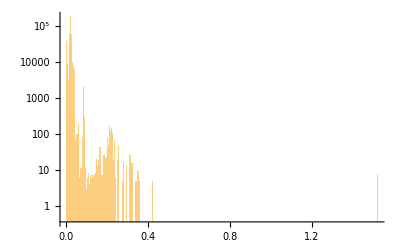

```mathematica
Histogram[%125,PlotRange->All,ScalingFunctions->"Log"]
```